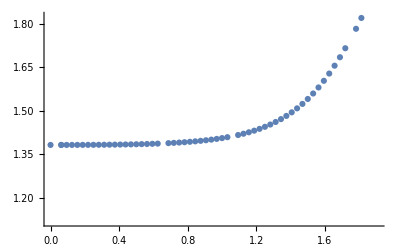

```mathematica
c4={{0,9.030202},{0.062500,9.023398},{0.062500,9.023398},{0.093750,9.074417},{0.125000,9.118160},{0.156250,9.165339},{0.187500,9.216783},{0.218750,9.272075},{0.250000,9.330591},{0.281250,9.391725},{0.312500,9.454933},{0.343750,9.519743},{0.375000,9.585755},{0.406250,9.652627},{0.437500,9.720076},{0.468750,9.787870},{0.500000,9.855822},{0.531250,9.923789},{0.562500,9.991668},{0.593750,10.059396},{0.625000,10.126949},{0.656250,10.194341},{0.687500,10.261621},{0.718750,10.328881},{0.750000,10.396251},{0.781250,10.463900},{0.812500,10.532042},{0.843750,10.600936},{0.875000,10.670886},{0.906250,10.742246},{0.937500,10.815424},{0.968750,10.890882},{1.000000,10.969142},{1.031250,11.050787},{1.062500,11.136467},{1.093750,11.226902},{1.125000,11.322884},{1.156250,11.425283},{1.187500,11.535051},{1.218750,11.653223},{1.250000,11.780922},{1.281250,11.919362},{1.312500,12.069848},{1.343750,12.233782},{1.375000,12.412661},{1.406250,12.608079},{1.437500,12.821724},{1.468750,13.055382},{1.500000,13.310935},{1.531250,13.590356},{1.562500,13.895715},{1.593750,14.229180},{1.625000,14.593022},{1.656250,14.989630},{1.687500,15.421534},{1.718750,15.891445},{1.750000,16.402307},{1.781250,16.957392},{1.812500,17.560416},{1.843750,18.215719},{1.875000,18.928487},{1.906250,19.705043}};
cc4={{0,7.647250},{0.062500,7.640438},{0.062500,7.640438},{0.093750,7.691436},{0.125000,7.735144},{0.156250,7.782273},{0.187500,7.833650},{0.218750,7.888855},{0.250000,7.947265},{0.281250,8.008268},{0.312500,8.071318},{0.343750,8.135942},{0.375000,8.201734},{0.406250,8.268351},{0.437500,8.335504},{0.468750,8.402956},{0.500000,8.470515},{0.531250,8.538032},{0.562500,8.605398},{0.593750,8.672543},{0.625000,8.739434},{0.656250,204.470917},{0.687500,8.872504},{0.718750,8.938803},{0.750000,9.005086},{0.781250,9.071511},{0.812500,9.138273},{0.843750,9.205613},{0.875000,9.273813},{0.906250,9.343206},{0.937500,9.414172},{0.968750,9.487145},{1.000000,9.562612},{1.031250,9.641121},{1.062500,478.157230},{1.093750,9.809764},{1.125000,9.901311},{1.156250,9.998736},{1.187500,10.102924},{1.218750,10.214839},{1.250000,10.335523},{1.281250,10.466103},{1.312500,10.607786},{1.343750,10.761865},{1.375000,10.929722},{1.406250,11.112824},{1.437500,11.312727},{1.468750,11.531077},{1.500000,11.769615},{1.531250,12.030180},{1.562500,12.314717},{1.593750,12.625297},{1.625000,12.964137},{1.656250,13.333632},{1.687500,13.736401},{1.718750,14.175320},{1.750000,57.515655},{1.781250,15.174238},{1.812500,15.739985},{1.843750,16.349764},{1.875000,16.988448},{1.906250,17.592082}};
C4=c4-cc4*Table[{0,1},{i,0,61}];
ListPlot[{C4}]
```

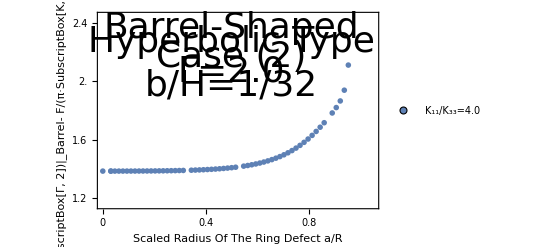

```mathematica
CC4=C4*Table[{0.5,1},{i,0,61}];
ListPlot[{CC4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{1.2,1.6,2.0,2.4},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.05},{1.15,2.45}},FrameLabel->{{"F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Barrel- F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Cylinder", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12}}],{Right, Bottom}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{0.5,2.37}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,2.27}],Text[Style["Case (2)",Directive[Black,36]],{0.5,2.17}],Text[Style["Γ=2.0",Directive[Black,36]],{0.5,2.07}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,1.97}]}]
```